# Clancey et al. Mechanistic Model (STOPPP)

## SIR Model with Waning Antibodies and Waning Immunity

N is the total population size, S is the number of susceptible individuals, Ι  is the number of infected individuals, R_A is the number of seropositive  and recovered individuals, and R_T is the number of seronegative and recovered individuals.

```mathematica
Ν̇=Ṡ+Ι̇+OverDot[RA] + OverDot[RT]
```

OverDot[RA]+OverDot[RT]+Ṡ+Ι̇

```mathematica
Ṡ=b Ν-β S Ι/Ν- S (μ+k Ν )+ Subscript[ω, T] RT
```

-(S β Ι)/Ν+b Ν-S (μ+k Ν)+RT ω_T

```mathematica
Ι̇=β S Ι/Ν-γ Ι - Ι(μ+k Ν )
```

-γ Ι+(S β Ι)/Ν-Ι (μ+k Ν)

```mathematica
OverDot[RA] =γ Ι- RA(μ+k Ν )- Subscript[ω, A] RA
```

γ Ι-RA (μ+k Ν)-RA ω_A

```mathematica
OverDot[RT]=Subscript[ω, A] RA- RT(μ+k Ν )- Subscript[ω, T] RT
```

-RT (μ+k Ν)+RA ω_A-RT ω_T

## Equilibria and ℛ_0

### Disease Free Equilibria (DFE)

```mathematica
Ν̇=FullSimplify[Ṡ+Ι̇+OverDot[RA]+OverDot[RT]]/.{RA+RT+S+Ι->Ν}
```

b Ν-Ν (μ+k Ν)

```mathematica
Solve[Ν̇==0, Ν]
```

{{Ν→0},{Ν→(b-μ)/k}}

```mathematica
Solve[(Ṡ/. {Ε->0,Ι->0,RA->0, RT->0})==0,S]/.{Ν->(b-μ)/k}
```

{{S→(b-μ)/k}}

```mathematica
DFE= {S->(b-μ)/k,Ε->0,Ι->0,RA->0, RT->0};
```

### Pathogen Present Equilibria

```mathematica
FullSimplify[Solve[{0==Ṡ, 0==Ι̇, 0==OverDot[RA] , 0==OverDot[RT]},{S,Ι, RA, RT}]/.{Ν->(b-μ)/k}]
```

{{S→(b-μ)/k,Ι→0,RA→0,RT→0},{S→((b+γ) (b-μ))/(k β),Ι→-((b-β+γ) (b-μ) (b+ω_A) (b+ω_T))/(k β ((b+γ) (b+ω_T)+ω_A (b+γ+ω_T))),RA→-(γ (b-β+γ) (b-μ) (b+ω_T))/(k β ((b+γ) (b+ω_T)+ω_A (b+γ+ω_T))),RT→-(γ (b-β+γ) (b-μ) ω_A)/(k β ((b+γ) (b+ω_T)+ω_A (b+γ+ω_T)))}}

## Calculate ℛ_0 using the Next Generation Method (NGM)

### Build vectors ℱ and 𝒱 to linearize the infection subsystem

ℱ represents the rate of appearance of new infections in compartment i, 𝒱_i^+(x) represents the rate of transfer of individuals into compartment i by all other means, and 𝒱_i^-(x) represents the rate of transfer of individuals out of compartment i, where 𝒱_i(x)=𝒱_i^-(x)  -𝒱_i^+(x). The infected compartments x={I} and the non-infected compartments are y={S,RA,RT}. Thus, this can be written as dx/dt=ℱ(x)-𝒱(x).

```mathematica
ℱ={β S Ι/Ν}
```

{(S β Ι)/Ν}

```mathematica
𝒱=-{-γ Ι -Ι(μ+k Ν )}
```

{γ Ι+Ι (μ+k Ν)}

### Find the Jacobian of ℱ and 𝒱 around the DFE

```mathematica
F=Grad[ℱ,{Ι}]
```

{{(S β)/Ν}}

```mathematica
Fdfe=F/.{S->Ν}
```

{{β}}

```mathematica
MatrixForm[Fdfe]
```

(β)

```mathematica
V=Grad[𝒱, {Ι}]
```

{{γ+μ+k Ν}}

```mathematica
Vdfe=V/.DFE
```

{{γ+μ+k Ν}}

```mathematica
MatrixForm[Vdfe]
```

(γ+μ+k Ν)

#### Take the inverse of 𝒱

```mathematica
Vinverse=Inverse[Vdfe]
```

{{1/(γ+μ+k Ν)}}

```mathematica
MatrixForm[Vinverse]
```

(1/(γ+μ+k Ν))

```mathematica
FVinverse=Fdfe.Vinverse
```

{{β/(γ+μ+k Ν)}}

```mathematica
MatrixForm[FVinverse]
```

(β/(γ+μ+k Ν))

## Solution for I as a Function of R_A

## Solution for I for the Mechanistic Model in Counts

#### ι̂(t) = (R_A (μ+k Ν+ ω_A)+OverDot[R_A])/γ

```mathematica
bfunc=g Exp[-s Cos[ π f t- ψ]^2]
```

ⅇ^(-s Cos[f π t-ψ]^2) g

```mathematica
bPars={g->0.004441452, s->4, f->1/365, ψ->1}
```

{g→0.00444145,s→4,f→1/365,ψ→1}

```mathematica
bave=N[Integrate[bfunc/.bPars,{t,0,365}]]/365
```

0.00137022

```mathematica
plottime=365*4
```

1460

```mathematica
Pars={b->bfunc/.bPars, β->.6,γ->1/10,μ->1/1095,k->(1/730-1/1095)/10000, Subscript[ω, A]->1/30, Subscript[ω, T]->1/180};
```

```mathematica
Sol1=NDSolve[{S'[t]==b Ν[t] -β S[t] Ι[t]/Ν[t]- S [t](μ+k Ν[t])+ Subscript[ω, T] RT[t],Ι'[t]==β S[t] Ι[t]/Ν[t]-γ Ι[t] - Ι[t](μ+k Ν[t] ),RA'[t]==γ Ι[t]- RA[t](μ+k Ν[t])- Subscript[ω, A] RA[t],RT'[t]==Subscript[ω, A] RA[t]- RT[t](μ+k Ν[t] )-Subscript[ω, T] RT[t],Ν'[t]==b Ν[t]-Ν[t] (μ+k Ν[t]),Ν[0]==10000,S[0]==9999,Ι[0]==1,RA[0]==0, RT[0]==0}/.Pars,{S[t],Ι[t],RA[t],RT[t],Ν[t]},{t,0,plottime}]
```

{{S[t]→InterpolatingFunction[…][t],Ι[t]→InterpolatingFunction[…][t],RA[t]→InterpolatingFunction[…][t],RT[t]→InterpolatingFunction[…][t],Ν[t]→InterpolatingFunction[…][t]}}

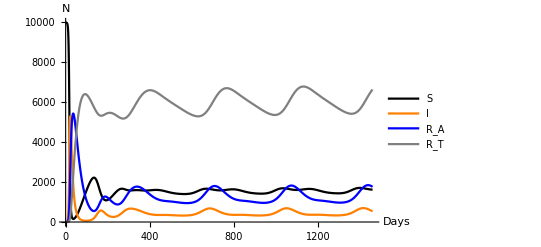

```mathematica
Plot[{S[t]/.Sol1,Ι[t]/.Sol1,RA[t]/.Sol1, RT[t]/.Sol1},{t,0,plottime},PlotLegends->{"S", "I", "R_A","R_T"}, PlotStyle->{Black, Orange, Blue, Gray}, AxesLabel->{Days, N}]
```

```mathematica
IPred= 1/γ(D[RA[t]/.Sol1,t]+(Subscript[ω, A] +μ + k((S[t]/.Sol1)+(Ι[t]/.Sol1)+(RA[t]/.Sol1)+(RT[t]/.Sol1))) RA[t]/.Sol1)/.Pars
```

{{10 (InterpolatingFunction[…][t] (5/146+1/21900000(InterpolatingFunction[…][t]+InterpolatingFunction[…][t]+InterpolatingFunction[…][t]+InterpolatingFunction[…][t]))+InterpolatingFunction[…][t])}}

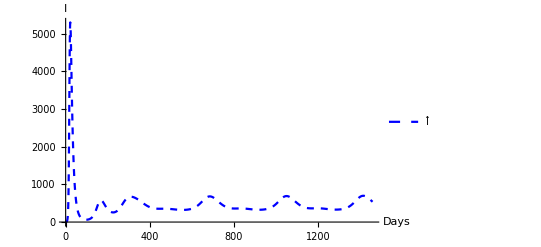

```mathematica
Pred=Plot[{IPred/.Sol1},{t,0,plottime},PlotStyle->{Blue,Dashed}, PlotRange->All, AxesLabel->{Days, Ι}, PlotLegends->{"Ι̂"} ]
```

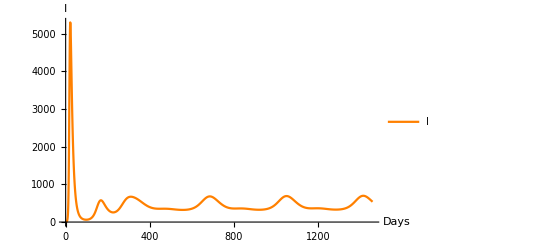

```mathematica
TRUE=Plot[{Ι[t]/.Sol1},{t,0,plottime}, PlotRange->All, PlotStyle->{Orange}, AxesLabel->{Days, Ι}, PlotLegends->{"I"}]
```

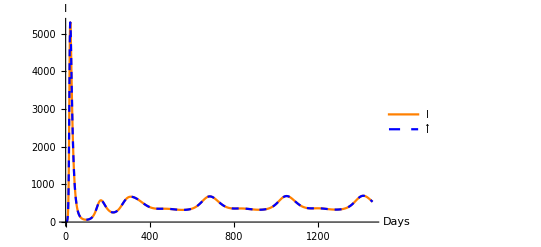

```mathematica
Show[TRUE, Pred]
```

## Solution for I for the Mechanistic Model in Proportions

N is the total population size, s is the number of susceptible individuals, ι  is the number of infected individuals, r_A is the number of seropositive  and recovered individuals, and r_T is the number of seronegative and recovered individuals.

### Change of Variables (COV) from Counts to Proportions using the quotient rule

```mathematica
ṡ=FullSimplify[FullSimplify[(Ṡ Ν-Ν̇ S)/Ν^2]/.{S->s Ν,Ι->ι Ν,RA->rA Ν, RT->rT Ν}]
```

b-b s-s β ι+rT ω_T

```mathematica
ι̇=FullSimplify[FullSimplify[(Ι̇ Ν-Ν̇ Ι)/Ν^2]/.{S->s Ν,Ι->ι Ν,RA->rA  Ν, RT->rT Ν}]
```

-((b-s β+γ) ι)

```mathematica
OverDot[rA]=FullSimplify[FullSimplify[(OverDot[RA] Ν-Ν̇ RA)/Ν^2]/.{S->s Ν,Ι->ι Ν,RA->rA  Ν, RT->rT Ν}]
```

-b rA+γ ι-rA ω_A

```mathematica
OverDot[rT]=FullSimplify[FullSimplify[(OverDot[RT] Ν-Ν̇ RT)/Ν^2]/.{S->s Ν,Ι->ι Ν,RA->rA Ν, RT->rT Ν}]
```

rA ω_A-rT (b+ω_T)

```mathematica
FullSimplify[ṡ+ι̇+OverDot[rA]+ OverDot[rT]]/.{rA+ rT+s+ι->1}
```

0

#### Check Proportion (COV) Solution Equals Count Solution

```mathematica
Sol2=NDSolve[{s'[t]==b-b s[t]-s[t] β ι[t]+rT[t] Subscript[ω, T],
ι'[t]==-ι[t] (b+γ-s[t] β),
rA'[t]==γ ι[t]-rA[t] (b+Subscript[ω, A]),
rT'[t]==rA[t] Subscript[ω, A]-rT[t](b+Subscript[ω, T]),
Ν'[t]==b Ν[t]-Ν[t] (μ+k Ν[t]),
Ν[0]==10000,s[0]==9999/Ν[0],ι[0]==1/Ν[0],rA[0]==0/Ν[0],rT[0]==0/Ν[0]}/.Pars,{s[t],ι[t],rA[t],rT[t],Ν[t]},{t,0,plottime}]
```

{{s[t]→InterpolatingFunction[…][t],ι[t]→InterpolatingFunction[…][t],rA[t]→InterpolatingFunction[…][t],rT[t]→InterpolatingFunction[…][t],Ν[t]→InterpolatingFunction[…][t]}}

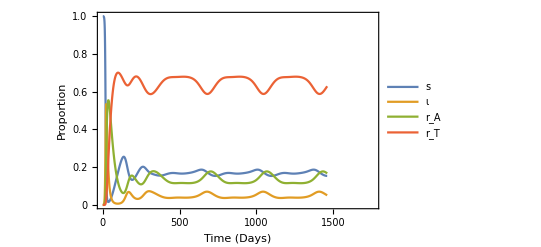

```mathematica
COVPlot=Plot[{s[t]/.Sol2,ι[t]/.Sol2,rA[t]/.Sol2, rT[t]/.Sol2},{t,0,plottime},PlotRange->{{0,plottime+300},{0,1}},PlotLegends->Placed[{"s", "ι", "r_A","r_T"}, {Right,Center}],  Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{{"Proportion",None},{"Time (Days)", None}},FrameTicks->All]
```

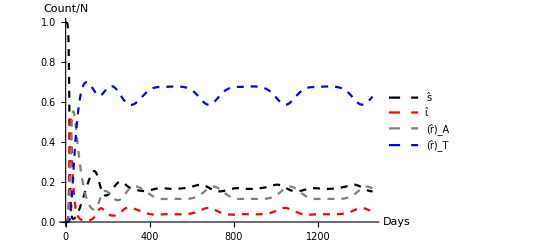

```mathematica
CountPlot=Plot[{S[t]/(S[t]+Ι[t]+RA[t]+RT[t])/.Sol1,Ι[t]/(S[t]+Ι[t]+RA[t]+RT[t])/.Sol1,RA[t]/(S[t]+Ι[t]+RA[t]+RT[t])/.Sol1,RT[t]/(S[t]+Ι[t]+RA[t]+RT[t])/.Sol1},{t,0,plottime},PlotLegends->{"ŝ", "ι̂", "(r̂)_A","(r̂)_T"}, AxesLabel->{Days, Count/N},PlotStyle->{{Black,Dashed},{Red,Dashed},{Gray,Dashed},{Blue,Dashed}}]
```

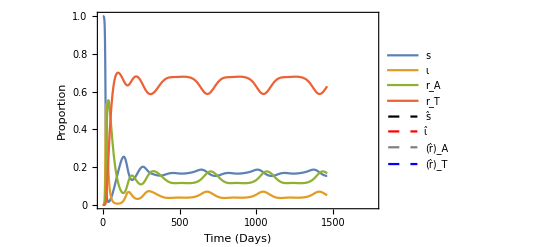

```mathematica
Show[{COVPlot,CountPlot}]
```

#### ι̂(t) = (r_A (b+ω_A)+OverDot[r_A])/γ

```mathematica
IPredProp= (D[rA[t]/.Sol2,t]+ (rA[t]/.Sol2 )(b+Subscript[ω, A]))/γ/.Pars
```

{10 ((1/30+0.00444145 ⅇ^(-4 Cos[1-(π t)/365]^2)) InterpolatingFunction[…][t]+InterpolatingFunction[…][t])}

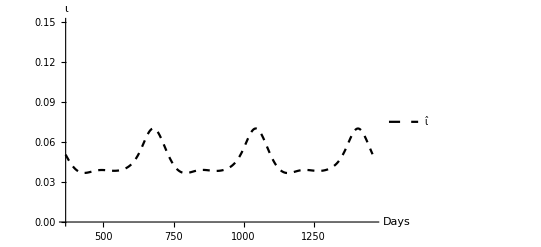

```mathematica
PredProp=Plot[{IPredProp},{t,365,plottime},PlotStyle->{Black,Dashed}, PlotRange->{{365,plottime},{0,0.15}}, AxesLabel->{Days, ι}, PlotLegends->Placed[{"ι̂"} , {Right,Top}]]
```

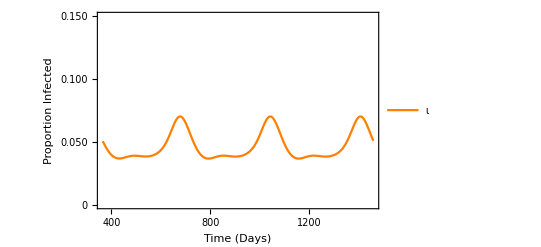

```mathematica
TRUEProp=Plot[{ι[t]/.Sol2},{t,365,plottime}, PlotRange->{{365,plottime},{0,0.15}}, PlotStyle->{Orange}, Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{"Proportion Infected",None},{"Time (Days)", None}},FrameTicks->All, PlotLegends->Placed[{"ι"}, {Right,Top}]]
```

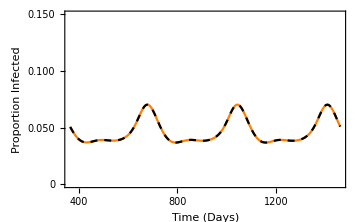

```mathematica
TrueBirth=Show[TRUEProp, PredProp]
```

#### The Solution for ι̂(t) can be approximated without the need for b(t) as long as the birth rate at any time point (t) is << ω_a.

```mathematica
IPredPropapprox= (D[rA[t]/.Sol2,t]+ (rA[t]/.Sol2 )Subscript[ω, A])/γ/.Pars
```

{10 (1/30 InterpolatingFunction[…][t]+InterpolatingFunction[…][t])}

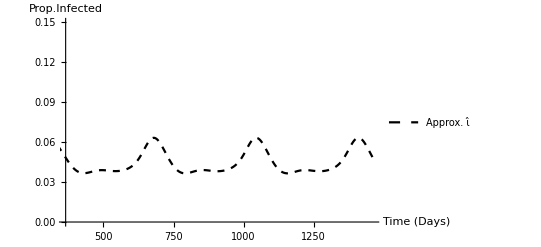

```mathematica
PredPropapprox=Plot[{IPredPropapprox},{t,0,plottime},PlotStyle->{Black,Dashed},PlotRange->{{365,plottime},{0,0.15}}, AxesLabel->{"Time (Days)", Prop. Infected}, PlotLegends->Placed[{"Approx. ι̂"} , {Right,Top}]]
```

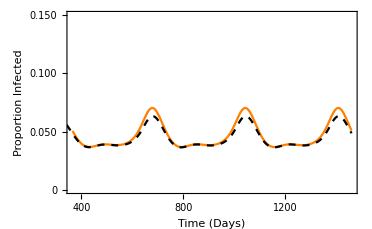

```mathematica
NoBirth=Show[TRUEProp, PredPropapprox]
```